```mathematica
Manipulate[StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{m*r+r^3-r^5,1/10+(1/2)*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],{m,-1/2,0},FrameLabel->{x,y}]
```

```mathematica
Manipulate[Plot[m*r+r^3-r^5,{r,0,2},PlotRange->{{0,2},{-1/2,1/2}},AxesLabel->{r,OverDot[r]}],{m,-1/2,0}]
```

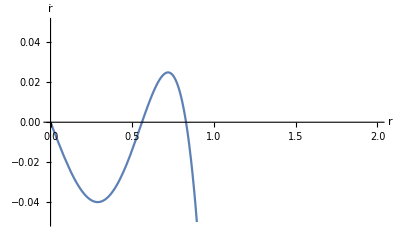

```mathematica
psnpbif=Plot[-0.215*r+r^3-r^5,{r,0,2},PlotRange->{{0,2},{-0.05,0.05}},AxesLabel->{r,OverDot[r]}]
```

```mathematica
Export["radial_s-n_postb.jpg",psnpbif,CompressionLevel->0]
```

radial_s-n_postb.jpg

```mathematica
pssn3=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.215*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn31=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.215*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{1,0}},StreamStyle->{Red,Thick},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn32=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.215*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{0.7,0}},StreamStyle->{Green,Thick},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn33=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.215*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{0.1,0}},StreamStyle->{Orange,Thick},FrameLabel->{x,y},StreamColorFunction->None];
```

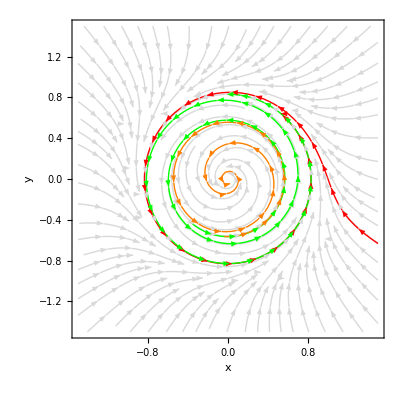

```mathematica
phspsnpb=Show[pssn3,pssn31,pssn32,pssn33]
```

```mathematica
Export["phsp_s-n_postb.jpg",phspsnpb,CompressionLevel->0]
```

phsp_s-n_postb.jpg

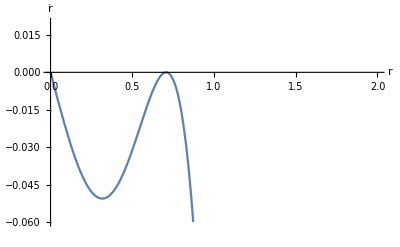

```mathematica
psnbif=Plot[-0.25*r+r^3-r^5,{r,0,2},PlotRange->{{0,2},{-0.06,0.02}},AxesLabel->{r,OverDot[r]}]
```

```mathematica
Export["radial_s-n_b.jpg",psnbif,CompressionLevel->0]
```

radial_s-n_b.jpg

```mathematica
pssn2=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.25*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn21=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.25*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{1,0}},StreamStyle->{Red,Thick},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn22=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.25*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{1/2,0}},StreamStyle->{Green,Thick},FrameLabel->{x,y},StreamColorFunction->None];
```

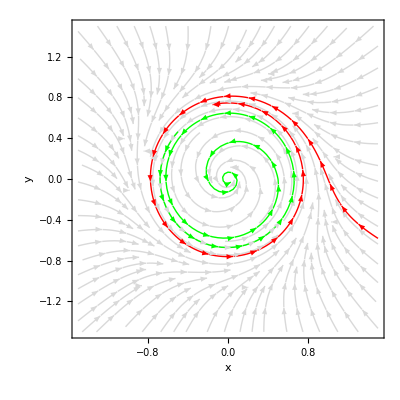

```mathematica
phspsnb=Show[pssn2,pssn21,pssn22]
```

```mathematica
Export["phsp_s-n_b.jpg",phspsnb,CompressionLevel->0]
```

phsp_s-n_b.jpg

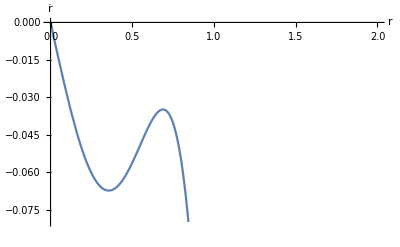

```mathematica
psnprbif=Plot[-0.3*r+r^3-r^5,{r,0,2},PlotRange->{{0,2},{-0.08,0}},AxesLabel->{r,OverDot[r]}]
```

```mathematica
Export["radial_s-n_preb.jpg",psnprbif,CompressionLevel->0]
```

radial_s-n_preb.jpg

```mathematica
pssn1=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.3*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pssn11=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.3*r+r^3-r^5,0.1+0.5*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Red,Thick},StreamPoints->{{0,1}},FrameLabel->{x,y},StreamColorFunction->None];
```

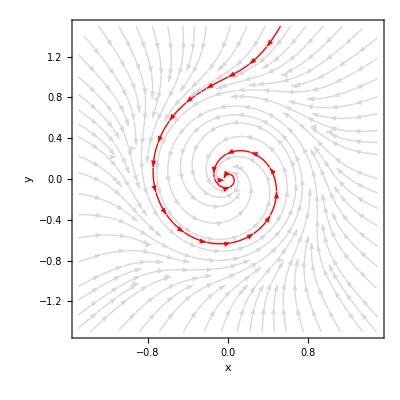

```mathematica
phspsnprb=Show[pssn1,pssn11]
```

```mathematica
Export["phsp_s-n_preb.jpg",phspsnprb,CompressionLevel->0]
```

phsp_s-n_preb.jpg

```mathematica
Manipulate[StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),m-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},FrameLabel->{x,y}],{m,0,2}]
```

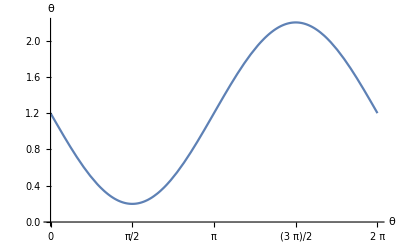

```mathematica
infppreb=Plot[1.2-Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{0,2.2}},AxesLabel->{θ,OverDot[θ]},Ticks->{{0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic}]
```

```mathematica
Export["angle_i-p_preb.jpg",infppreb,CompressionLevel->0]
```

angle_i-p_preb.jpg

```mathematica
psip1=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip11=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Red,Thick},StreamPoints->{{-1,-1}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip12=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Green,Thick},StreamPoints->{{0,-1/2}},FrameLabel->{x,y},StreamColorFunction->None];
```

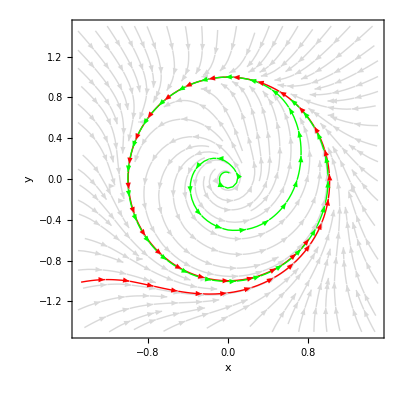

```mathematica
phspipprb=Show[psip1,psip11,psip12]
```

```mathematica
Export["phsp_i-p_preb.jpg",phspipprb,CompressionLevel->0]
```

phsp_i-p_preb.jpg

```mathematica
sipb1=NDSolve[{r'[t]==r[t]*(1-r[t]^2),a'[t]==1.2-Sin[a[t]],r[0]==2,a[0]==0},{r,a},{t,0,1000}];
```

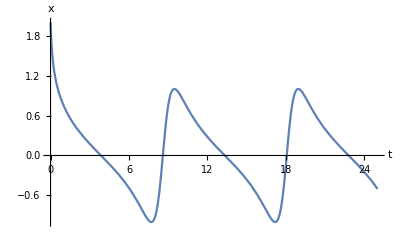

```mathematica
ipsolpreb=Plot[Evaluate[r[t]*Cos[a[t]]/.sipb1],{t,0,25},AxesLabel->{t,x}]
```

```mathematica
Export["sol_i-p_preb.jpg",ipsolpreb,CompressionLevel->0]
```

sol_i-p_preb.jpg

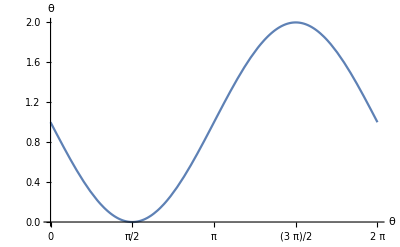

```mathematica
infppb=Plot[1-Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{0,2}},AxesLabel->{θ,OverDot[θ]},Ticks->{{0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic}]
```

```mathematica
Export["angle_i-p_pb.jpg",infppb,CompressionLevel->0]
```

angle_i-p_pb.jpg

```mathematica
psip2=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip21=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Red,Thick},StreamPoints->{{0,1.01}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip22=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Green,Thick},StreamPoints->{{0,0.99}},FrameLabel->{x,y},StreamColorFunction->None];
psip23=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Orange,Thick},StreamPoints->{{-0.3,1}},FrameLabel->{x,y},StreamColorFunction->None];
```

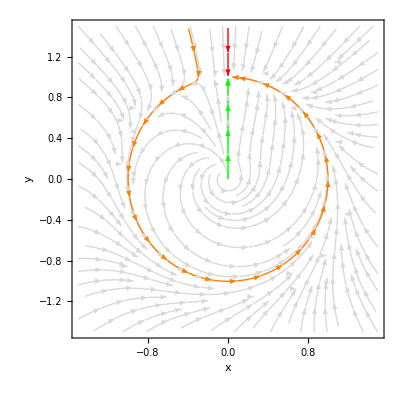

```mathematica
phspipb=Show[psip2,psip21,psip22,psip23]
```

```mathematica
Export["phsp_i-p_b.jpg",phspipb,CompressionLevel->0]
```

phsp_i-p_b.jpg

```mathematica
sipb2=NDSolve[{r'[t]==r[t]*(1-r[t]^2),a'[t]==1-Sin[a[t]],r[0]==1,a[0]==Pi/2+0.01},{r,a},{t,0,1000}];
```

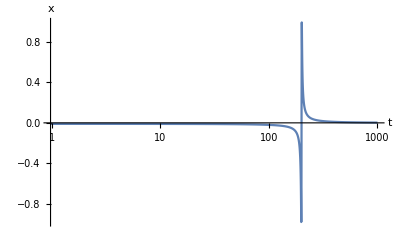

```mathematica
LogLinearPlot[Evaluate[r[t]*Cos[a[t]]/.sipb2],{t,0,1000},AxesLabel->{"t",x},PlotRange->All]
```

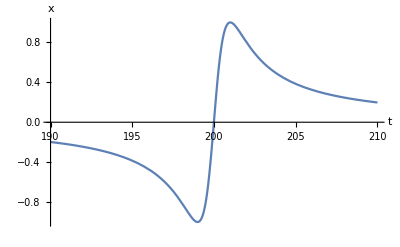

```mathematica
ipsolb=Plot[Evaluate[r[t]*Cos[a[t]]/.sipb2],{t,190,210},AxesLabel->{"t",x},PlotRange->All]
```

```mathematica
Export["sol_i-p_b.jpg",ipsolb,CompressionLevel->0]
```

sol_i-p_b.jpg

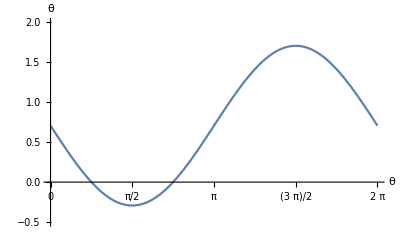

```mathematica
infppostb=Plot[Sqrt[2]/2-Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{-1/2,2}},AxesLabel->{θ,OverDot[θ]},Ticks->{{0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic}]
```

```mathematica
Export["angle_i-p_postb.jpg",infppostb,CompressionLevel->0]
```

angle_i-p_postb.jpg

```mathematica
psip3=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip31=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Red,Thick},StreamPoints->{{-1.1,1}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip32=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Green,Thick},StreamPoints->{{-0.5,1}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip33=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Pink,Thick},StreamPoints->{{-0.11,0.1}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
psip34=StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamStyle->{Blue,Thick},StreamPoints->{{-0.4,0.5}},FrameLabel->{x,y},StreamColorFunction->None];
```

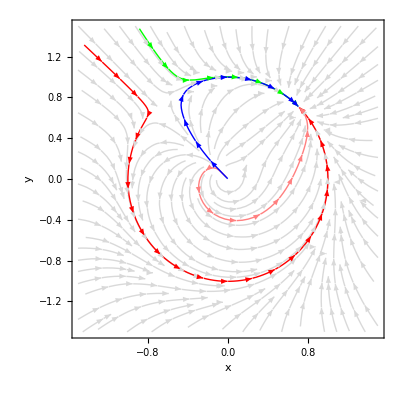

```mathematica
phspippostb=Show[psip3,psip31,psip32,psip33,psip34]
```

```mathematica
Export["phsp_i-p_postbif.jpg",phspippostb,CompressionLevel->0]
```

phsp_i-p_postbif.jpg

```mathematica
sipb3=NDSolve[{r'[t]==r[t]*(1-r[t]^2),a'[t]==Sqrt[2]/2-Sin[a[t]],r[0]==2.05,a[0]==3*Pi/4+0.01},{r,a},{t,0,1000}];
```

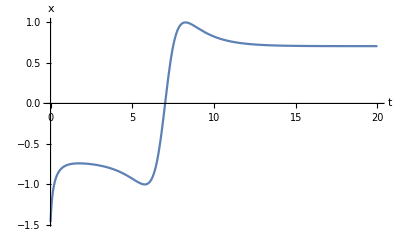

```mathematica
ipsolposb=Plot[Evaluate[r[t]*Cos[a[t]]/.sipb3],{t,0,20},AxesLabel->{"t",x},PlotRange->All]
```

```mathematica
Export["sol_i-p_postbif.jpg",ipsolposb,CompressionLevel->0]
```

sol_i-p_postbif.jpg

```mathematica
Manipulate[StreamPlot[{y,m*y+x-x^2+x*y},{x,-2,2},{y,-2,2},FrameLabel->{x,y}],{m,-1,-0.5}]
```

```mathematica
pshb1=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pshb11=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Red,Thick},StreamPoints->{{0.0837,0.0546}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pshb12=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Green,Thick},StreamPoints->{{-1,1}},FrameLabel->{x,y},StreamColorFunction->None];
```

```mathematica
pshb13=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Blue,Thick},StreamPoints->{{1.9,0}},FrameLabel->{x,y},StreamColorFunction->None];
pshb14=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Black,Thick},StreamPoints->{{0.0546,-0.0837}},FrameLabel->{x,y},StreamColorFunction->None];
pshb15=StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Pink,Thick},StreamPoints->{{1,-0.6}},FrameLabel->{x,y},StreamColorFunction->None];
```

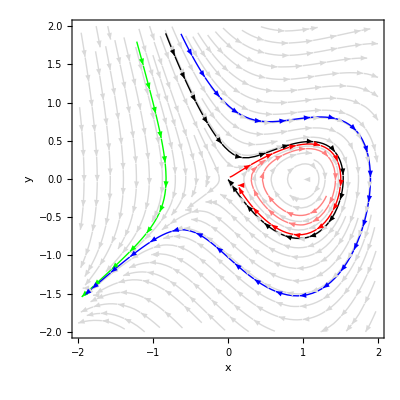

```mathematica
phsphopreb=Show[pshb1,pshb11,pshb12,pshb13,pshb14,pshb15]
```

```mathematica
Export["phsp_homoc_prebif.jpg",phsphopreb,CompressionLevel->0]
```

phsp_homoc_prebif.jpg

```mathematica
Eigensystem[{{0,1},{1,-0.88}}]
```

{{-1.53252,0.65252},{{-0.546471,0.837478},{-0.837478,-0.546471}}}

```mathematica
shb1=NDSolve[{x'[t]==y[t],y'[t]==-0.88*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.98,y[0]==0.01},{x,y},{t,0,1000}];
```

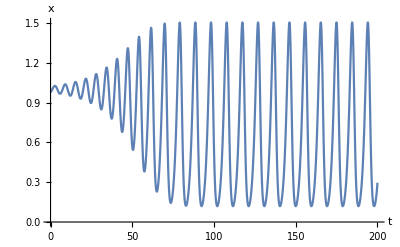

```mathematica
solhopreb=Plot[Evaluate[x[t]/.shb1],{t,0,200},AxesLabel->{t,x}]
```

```mathematica
Export["sol_homoc_prebif.jpg",solhopreb,CompressionLevel->0]
```

sol_homoc_prebif.jpg

```mathematica
pshb2=StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
pshb21=StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Red,Thick},StreamPoints->{{0.0835,0.0549}},FrameLabel->{x,y},StreamColorFunction->None];
pshb22=StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Green,Thick},StreamPoints->{{-1,1}},FrameLabel->{x,y},StreamColorFunction->None];
pshb23=StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Blue,Thick},StreamPoints->{{1.9,0}},FrameLabel->{x,y},StreamColorFunction->None];
pshb24=StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Pink,Thick},StreamPoints->{{1,-0.6}},FrameLabel->{x,y},StreamColorFunction->None];
```

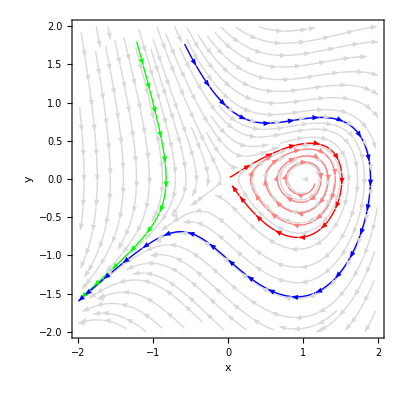

```mathematica
phsphob=Show[pshb2,pshb21,pshb22,pshb23,pshb24]
```

```mathematica
Export["phsp_homoc_bif.jpg",phsphob,CompressionLevel->0]
```

phsp_homoc_bif.jpg

```mathematica
Eigensystem[{{0,1},{1,-0.865}}]
```

{{-1.52202,0.657021},{{-0.549107,0.835752},{-0.835752,-0.549107}}}

```mathematica
shb2=NDSolve[{x'[t]==y[t],y'[t]==-0.8645*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.98,y[0]==0.01},{x,y},{t,0,1000}];
```

NDSolve::nderr: Error test failure at t == 118.481; unable to continue.

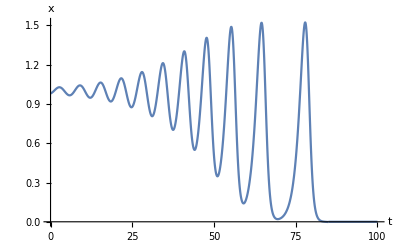

```mathematica
solhob=Show[Plot[Piecewise[{{Evaluate[x[t]/.shb2],t<85},{0,t≥85}}],{t,0,100},AxesLabel->{t,x}],Plot[0,{t,85,100}]]
```

```mathematica
Export["sol_homoc_bif.jpg",solhob,CompressionLevel->0]
```

sol_homoc_bif.jpg

```mathematica
pshb3=StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->LightGray,FrameLabel->{x,y},StreamColorFunction->None];
pshb31=StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Red,Thick},StreamPoints->{{0.0835,0.0549}},FrameLabel->{x,y},StreamColorFunction->None];
pshb32=StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Green,Thick},StreamPoints->{{-1,1}},FrameLabel->{x,y},StreamColorFunction->None];
pshb33=StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Blue,Thick},StreamPoints->{{1.9,0}},FrameLabel->{x,y},StreamColorFunction->None];
pshb34=StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamStyle->{Black,Thick},StreamPoints->{{0.0555,-0.0831}},FrameLabel->{x,y},StreamColorFunction->None];
```

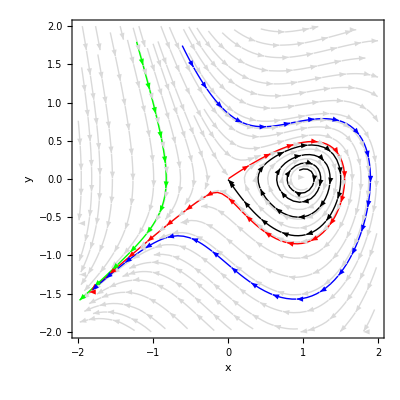

```mathematica
phsphoposb=Show[pshb3,pshb31,pshb32,pshb33,pshb34]
```

```mathematica
Export["phsp_homoc_postbif.jpg",phsphoposb,CompressionLevel->0]
```

phsp_homoc_postbif.jpg

```mathematica
Eigensystem[{{0,1},{1,-0.83}}]
```

{{-1.49769,0.667693},{{-0.555291,0.831656},{-0.831656,-0.555291}}}

```mathematica
shb3=NDSolve[{x'[t]==y[t],y'[t]==-0.83*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.98,y[0]==0.01},{x,y},{t,0,1000}];
```

NDSolve::nderr: Error test failure at t == 84.9656; unable to continue.

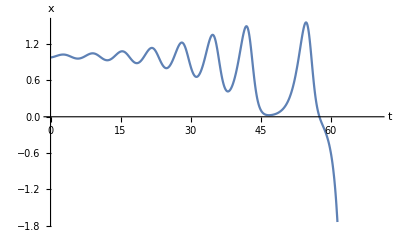

```mathematica
solhoposb=Plot[Evaluate[x[t]/.shb3],{t,0,70},AxesLabel->{t,x}]
```

```mathematica
Export["sol_homoc_postbif.jpg",solhoposb,CompressionLevel->0]
```

sol_homoc_postbif.jpg